# Examples of using LePDF

Authors: F.Garosi, D.Marzocca and S.Trifinopoulos
Date: 21/10/2024

```mathematica
Quit[]
```

## Selecting Options

**************************************************
Choose the electron or muon:

```mathematica
lepton="muon";
(*lepton="electron";*)
```

Choose the number of Flavour Scheme you want:

```mathematica
FS="5FS";
(*FS="6FS";*)
```

Choose the order for interpolating LePDFs over the xGrid.
By default, for general use, this is set to 1.
Setting it to 0 allows to perform integrals of PDFs (for instance for conservation sum rules) with rectangles method, consistent with the method used in the derivation.

```mathematica
xGridInterpolationOrder=1;
```

## Import PDFs

### Input parameters

```mathematica
lepton
```

muon

```mathematica
TeV=10^3;
GeV=1;
MeV=10^-3;
keV=10^-6;
eV=10^-9;
```

```mathematica
me=0.510998950 MeV;
mμ=105.6584 MeV;
```

```mathematica
If[lepton=="muon",
m0=mμ ;,
m0=me;
]
```

```mathematica
m0
```

0.105658

### Particle IDs

```mathematica
ParticleTable6FS=({{eL, "eL", 11, "-"}, {eR, "eR", 11, "+"}, {νe, "nue", 12, "-"}, {μL, "muL", 13, "-"}, {μR, "muR", 13, "+"}, {νμ, "numu", 14, "-"}, {τL, "taL", 15, "-"}, {τR, "taR", 15, "+"}, {ντ, "nuta", 16, "-"}, {eLb, "eLb", -11, "+"}, {eRb, "eRb", -11, "-"}, {νeb, "nueb", -12, "+"}, {μLb, "muLb", -13, "+"}, {μRb, "muRb", -13, "-"}, {νμb, "numub", -14, "+"}, {τLb, "taLb", -15, "+"}, {τRb, "taRb", -15, "-"}, {ντb, "nutab", -16, "+"}, {dL, "dL", 1, "-"}, {dR, "dR", 1, "+"}, {uL, "uL", 2, "-"}, {uR, "uR", 2, "+"}, {sL, "sL", 3, "-"}, {sR, "sR", 3, "+"}, {cL, "cL", 4, "-"}, {cR, "cR", 4, "+"}, {bL, "bL", 5, "-"}, {bR, "bR", 5, "+"}, {tL, "tL", 6, "-"}, {tR, "tR", 6, "+"}, {dLb, "dLb", -1, "+"}, {dRb, "dRb", -1, "-"}, {uLb, "uLb", -2, "+"}, {uRb, "uRb", -2, "-"}, {sLb, "sLb", -3, "+"}, {sRb, "sRb", -3, "-"}, {cLb, "cLb", -4, "+"}, {cRb, "cRb", -4, "-"}, {bLb, "bLb", -5, "+"}, {bRb, "bRb", -5, "-"}, {tLb, "tLb", -6, "+"}, {tRb, "tRb", -6, "-"}, {gp, "gp", 21, "+"}, {gm, "gm", 21, "-"}, {γp, "gap", 22, "+"}, {γm, "gam", 22, "-"}, {Zp, "Zp", 23, "+"}, {Zm, "Zm", 23, "-"}, {ZL, "ZL", 23, 0}, {Zγp, "Zgap", 2223, "+"}, {Zγm, "Zgam", 2223, "-"}, {Wpp, "Wpp", 24, "+"}, {Wpm, "Wpm", 24, "-"}, {WpL, "WpL", 24, 0}, {Wmp, "Wmp", -24, "+"}, {Wmm, "Wmm", -24, "-"}, {WmL, "WmL", -24, 0}, {h, "h", 25, 0}, {hZL, "hZL", 2523, 0}});
```

```mathematica
ParticleList6FS=ParticleTable6FS[[;;,1]]
```

{eL,eR,νe,μL,μR,νμ,τL,τR,ντ,eLb,eRb,νeb,μLb,μRb,νμb,τLb,τRb,ντb,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,tL,tR,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,tLb,tRb,gp,gm,γp,γm,Zp,Zm,ZL,Zγp,Zγm,Wpp,Wpm,WpL,Wmp,Wmm,WmL,h,hZL}

```mathematica
ParticleTable5FS=({{eL, "eL", 11, "-"}, {eR, "eR", 11, "+"}, {νe, "nue", 12, "-"}, {μL, "muL", 13, "-"}, {μR, "muR", 13, "+"}, {νμ, "numu", 14, "-"}, {τL, "taL", 15, "-"}, {τR, "taR", 15, "+"}, {ντ, "nuta", 16, "-"}, {eLb, "eLb", -11, "+"}, {eRb, "eRb", -11, "-"}, {νeb, "nueb", -12, "+"}, {μLb, "muLb", -13, "+"}, {μRb, "muRb", -13, "-"}, {νμb, "numub", -14, "+"}, {τLb, "taLb", -15, "+"}, {τRb, "taRb", -15, "-"}, {ντb, "nutab", -16, "+"}, {dL, "dL", 1, "-"}, {dR, "dR", 1, "+"}, {uL, "uL", 2, "-"}, {uR, "uR", 2, "+"}, {sL, "sL", 3, "-"}, {sR, "sR", 3, "+"}, {cL, "cL", 4, "-"}, {cR, "cR", 4, "+"}, {bL, "bL", 5, "-"}, {bR, "bR", 5, "+"}, {dLb, "dLb", -1, "+"}, {dRb, "dRb", -1, "-"}, {uLb, "uLb", -2, "+"}, {uRb, "uRb", -2, "-"}, {sLb, "sLb", -3, "+"}, {sRb, "sRb", -3, "-"}, {cLb, "cLb", -4, "+"}, {cRb, "cRb", -4, "-"}, {bLb, "bLb", -5, "+"}, {bRb, "bRb", -5, "-"}, {gp, "gp", 21, "+"}, {gm, "gm", 21, "-"}, {γp, "gap", 22, "+"}, {γm, "gam", 22, "-"}, {Zp, "Zp", 23, "+"}, {Zm, "Zm", 23, "-"}, {ZL, "ZL", 23, 0}, {Zγp, "Zgap", 2223, "+"}, {Zγm, "Zgam", 2223, "-"}, {Wpp, "Wpp", 24, "+"}, {Wpm, "Wpm", 24, "-"}, {WpL, "WpL", 24, 0}, {Wmp, "Wmp", -24, "+"}, {Wmm, "Wmm", -24, "-"}, {WmL, "WmL", -24, 0}, {h, "h", 25, 0}, {hZL, "hZL", 2523, 0}});
```

```mathematica
ParticleList5FS=ParticleTable5FS[[;;,1]]
```

{eL,eR,νe,μL,μR,νμ,τL,τR,ντ,eLb,eRb,νeb,μLb,μRb,νμb,τLb,τRb,ντb,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,gp,gm,γp,γm,Zp,Zm,ZL,Zγp,Zγm,Wpp,Wpm,WpL,Wmp,Wmm,WmL,h,hZL}

```mathematica
If[FS=="6FS",
ParticleTable=ParticleTable6FS;
ParticleList=ParticleList6FS;,
ParticleTable=ParticleTable5FS;
ParticleList=ParticleList5FS;
]
```

```mathematica
ParticleList
```

{eL,eR,νe,μL,μR,νμ,τL,τR,ντ,eLb,eRb,νeb,μLb,μRb,νμb,τLb,τRb,ντb,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,gp,gm,γp,γm,Zp,Zm,ZL,Zγp,Zγm,Wpp,Wpm,WpL,Wmp,Wmm,WmL,h,hZL}

### Load the Lepton PDF

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
lepton
```

muon

```mathematica
If[lepton=="muon",
If[FS=="6FS",
μFileTable=Import["LePDF_mu_6FS_0000.dat"];,
μFileTable=Import["LePDF_mu_5FS_0000.dat"];;
],
If[FS=="6FS",
μFileTable=Import["LePDF_e_6FS_0000.dat"];,
μFileTable=Import["LePDF_e_5FS_0000.dat"];;
]
]
```

```mathematica
μFileTable[[1;;3]]//MatrixForm
```

({PdfType:,central}
{Format:,lhagrid1}
{---})

```mathematica
xGrid=μFileTable[[4]]
```

{1.×10^-6,1.18773×10^-6,1.40889×10^-6,1.66907×10^-6,1.97476×10^-6,2.33345×10^-6,2.75376×10^-6,3.24563×10^-6,3.8205×10^-6,4.49149×10^-6,5.27364×10^-6,6.18419×10^-6,7.24283×10^-6,8.47204×10^-6,9.89746×10^-6,0.0000115483,0.0000134577,0.0000156633,0.0000182078,0.0000211396,0.0000245132,0.0000283902,0.0000328402,0.0000379414,0.0000437815,0.0000504592,0.000058085,0.0000667826,0.0000766901,0.0000879616,0.000100769,0.000115304,0.000131778,0.000150427,0.000171512,0.000195321,0.000222175,0.000252425,0.000286457,0.0003247,0.00036762,0.000415732,0.000469599,0.000529834,0.00059711,0.000672158,0.000755778,0.000848835,0.00095227,0.0010671,0.00119444,0.00133547,0.00149149,0.00166388,0.00185413,0.00206385,0.00229476,0.00254871,0.00282766,0.00313371,0.00346912,0.00383627,0.0042377,0.00467609,0.00515432,0.00567538,0.00624248,0.00685896,0.00752838,0.00825443,0.00904102,0.00989224,0.0108123,0.0118058,0.0128772,0.0140315,0.0152735,0.0166086,0.018042,0.0195793,0.0212261,0.0229885,0.0248723,0.0268837,0.029029,0.0313146,0.033747,0.0363328,0.0390786,0.0419913,0.0450775,0.0483441,0.0517979,0.0554456,0.0592939,0.0633497,0.0676193,0.0721093,0.0768261,0.0817757,0.0869641,0.092397,0.0980799,0.104018,0.110216,0.116679,0.12341,0.130414,0.137694,0.145253,0.153092,0.161215,0.169622,0.178314,0.187291,0.196554,0.2061,0.215929,0.226038,0.236424,0.247083,0.258011,0.269204,0.280655,0.292358,0.304306,0.316491,0.328905,0.341539,0.354382,0.367425,0.380655,0.394063,0.407634,0.421357,0.435218,0.449203,0.463298,0.477488,0.491758,0.506092,0.520475,0.53489,0.549321,0.563752,0.578165,0.592544,0.606872,0.621132,0.635307,0.649382,0.663338,0.67716,0.690831,0.704337,0.71766,0.730786,0.743701,0.756389,0.768837,0.781032,0.792961,0.804612,0.815973,0.827033,0.837784,0.848214,0.858315,0.86808,0.877502,0.886573,0.89529,0.903646,0.911638,0.919263,0.926519,0.933405,0.93992,0.946066,0.951842,0.957252,0.95829,0.959314,0.960323,0.961318,0.962299,0.963265,0.964216,0.965154,0.966077,0.966986,0.96788,0.968761,0.969627,0.97048,0.971318,0.972142,0.972953,0.973749,0.974532,0.975301,0.976057,0.976799,0.977527,0.978241,0.978942,0.97963,0.980305,0.980966,0.981614,0.982249,0.982871,0.983479,0.984075,0.984658,0.985229,0.985786,0.986331,0.986864,0.987384,0.987891,0.988387,0.98887,0.989341,0.9898,0.990247,0.990682,0.991106,0.991517,0.991918,0.992307,0.992684,0.99305,0.993406,0.99375,0.994083,0.994405,0.994717,0.995018,0.995309,0.995589,0.995859,0.996119,0.996369,0.996609,0.996839,0.997059,0.997271,0.997472,0.997665,0.997849,0.998023,0.998189,0.998346,0.998495,0.998636,0.998768,0.998892,0.999009,0.999117,0.999219,0.999313,0.9994,0.99948,0.999553,0.999619,0.99968,0.999734,0.999782,0.999825,0.999862,0.999894,0.999921,0.999943,0.999961,0.999976,0.999986,0.999993,0.999998,1.,1.}

```mathematica
Nx=Length[xGrid]
```

281

```mathematica
δx=Join[{xGrid[[1]]},Table[xGrid[[i]]-xGrid[[i-1]],{i,2,Nx}]]
```

{1.×10^-6,1.87733×10^-7,2.21156×10^-7,2.60183×10^-7,3.05691×10^-7,3.58685×10^-7,4.2031×10^-7,4.91875×10^-7,5.7487×10^-7,6.70988×10^-7,7.82153×10^-7,9.10546×10^-7,1.05864×10^-6,1.22921×10^-6,1.42542×10^-6,1.65082×10^-6,1.90939×10^-6,2.20561×10^-6,2.54453×10^-6,2.93175×10^-6,3.37359×10^-6,3.87707×10^-6,4.45001×10^-6,5.10113×10^-6,5.84012×10^-6,6.67772×10^-6,7.62581×10^-6,8.69756×10^-6,9.90748×10^-6,0.0000112716,0.0000128075,0.0000145345,0.0000164739,0.000018649,0.000021085,0.0000238099,0.0000268537,0.0000302494,0.0000340328,0.0000382425,0.0000429205,0.0000481121,0.0000538661,0.0000602352,0.0000672759,0.0000750489,0.0000836194,0.0000930567,0.000103435,0.000114834,0.000127336,0.000141033,0.000156017,0.000172388,0.000190253,0.000209722,0.000230912,0.000253945,0.000278948,0.000306056,0.000335408,0.000367148,0.000401426,0.000438398,0.000478223,0.000521066,0.000567096,0.000616486,0.000669412,0.000726054,0.000786594,0.000851217,0.000920106,0.000993449,0.00107143,0.00115424,0.00124205,0.00133504,0.0014334,0.0015373,0.00164689,0.00176234,0.0018838,0.00201142,0.00214531,0.0022856,0.00243239,0.00258579,0.00274585,0.00291265,0.00308622,0.00326659,0.00345376,0.0036477,0.00384838,0.00405572,0.00426965,0.00449003,0.00471674,0.00494959,0.00518839,0.00543292,0.00568291,0.00593809,0.00619815,0.00646273,0.00673147,0.00700397,0.00727981,0.00755852,0.00783962,0.00812261,0.00840696,0.0086921,0.00897745,0.00926243,0.0095464,0.00982873,0.0101088,0.0103859,0.0106593,0.0109285,0.0111926,0.0114511,0.0117031,0.011948,0.0121852,0.0124139,0.0126335,0.0128432,0.0130425,0.0132308,0.0134073,0.0135715,0.013723,0.013861,0.0139852,0.014095,0.01419,0.0142699,0.0143342,0.0143827,0.014415,0.014431,0.0144304,0.0144131,0.014379,0.014328,0.0142602,0.0141756,0.0140742,0.0139563,0.013822,0.0136715,0.0135052,0.0133233,0.0131262,0.0129144,0.0126882,0.0124482,0.0121949,0.0119289,0.0116508,0.0113612,0.0110607,0.0107502,0.0104302,0.0101016,0.00976508,0.00942145,0.00907151,0.00871608,0.008356,0.00799209,0.00762522,0.00725623,0.006886,0.00651538,0.00614525,0.00577647,0.00540993,0.00103826,0.00102374,0.00100926,0.000994814,0.000980397,0.000966015,0.000951669,0.00093736,0.00092309,0.000908861,0.000894672,0.000880527,0.000866426,0.000852371,0.000838363,0.000824403,0.000810493,0.000796635,0.000782829,0.000769078,0.000755382,0.000741743,0.000728163,0.000714642,0.000701183,0.000687786,0.000674454,0.000661187,0.000647987,0.000634855,0.000621793,0.000608803,0.000595885,0.000583041,0.000570274,0.000557583,0.000544971,0.00053244,0.00051999,0.000507623,0.000495341,0.000483145,0.000471037,0.000459019,0.000447091,0.000435256,0.000423516,0.000411871,0.000400323,0.000388875,0.000377528,0.000366283,0.000355142,0.000344108,0.000333181,0.000322364,0.000311659,0.000301067,0.00029059,0.000280231,0.000269992,0.000259873,0.000249879,0.00024001,0.000230269,0.000220658,0.00021118,0.000201837,0.000192632,0.000183568,0.000174646,0.00016587,0.000157243,0.000148768,0.000140448,0.000132286,0.000124287,0.000116453,0.000108789,0.0001013,0.0000939887,0.0000868609,0.0000799217,0.0000731766,0.0000666317,0.0000602936,0.0000541695,0.0000482674,0.0000425962,0.000037166,0.0000319882,0.0000270759,0.0000224445,0.0000181125,0.0000141022,0.0000104421,7.16988×10^-6,4.33895×10^-6,2.03451×10^-6,4.3688×10^-7}

```mathematica
iTox[i_]:=xGrid[[i]];

xToi[x_]:=Position[xGrid,Nearest[xGrid,x][[1]]][[1,1]];
```

```mathematica
QGrid=μFileTable[[5]]
```

{9.9438,12.1336,14.8056,18.0661,22.0445,26.8991,32.8228,40.0509,48.8708,59.633,72.7653,80.379,98.0798,119.679,146.034,178.193,217.435,265.317,323.745,395.039,482.033,588.185,717.714,875.767,1068.63,1303.96,1591.11,1941.5,2369.05,2890.76,3527.35,4304.13,5251.98,6408.55,7819.83,9541.89,11643.2,14207.2,17335.9,21153.5,25811.9,31496.1,38432.1,46895.6,57222.8}

```mathematica
NQ=Length[QGrid]
```

45

```mathematica
tGrid=Log[QGrid^2/m0^2]
```

{9.08899,9.48704,9.8851,10.2832,10.6812,11.0793,11.4773,11.8754,12.2734,12.6715,13.0696,13.2686,13.6667,14.0647,14.4628,14.8608,15.2589,15.6569,16.055,16.4531,16.8511,17.2492,17.6472,18.0453,18.4433,18.8414,19.2395,19.6375,20.0356,20.4336,20.8317,21.2298,21.6278,22.0259,22.4239,22.822,23.22,23.6181,24.0162,24.4142,24.8123,25.2103,25.6084,26.0064,26.4045}

```mathematica
ParticlePDFList=μFileTable[[6]]
```

{eL,eR,nue,muL,muR,numu,taL,taR,nuta,eLb,eRb,nueb,muLb,muRb,numub,taLb,taRb,nutab,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,gp,gm,gap,gam,Zp,Zm,ZL,Zgap,Zgam,Wpp,Wpm,WpL,Wmp,Wmm,WmL,h,hZL}

```mathematica
NParticle=Length[ParticlePDFList]
```

55

```mathematica
PDGidList=μFileTable[[7]]
```

{11,11,12,13,13,14,15,15,16,-11,-11,-12,-13,-13,-14,-15,-15,-16,1,1,2,2,3,3,4,4,5,5,-1,-1,-2,-2,-3,-3,-4,-4,-5,-5,21,21,22,22,23,23,23,2223,2223,24,24,24,-24,-24,-24,25,2523}

```mathematica
ChiralityList=μFileTable[[8]]
```

{-,+,-,-,+,-,-,+,-,+,-,+,+,-,+,+,-,+,-,+,-,+,-,+,-,+,-,+,+,-,+,-,+,-,+,-,+,-,+,-,+,-,+,-,0,+,-,+,-,0,+,-,0,0,0}

```mathematica
{ParticlePDFList,PDGidList,ChiralityList}//MatrixForm
```

(eL | eR | nue | muL | muR | numu | taL | taR | nuta | eLb | eRb | nueb | muLb | muRb | numub | taLb | taRb | nutab | dL | dR | uL | uR | sL | sR | cL | cR | bL | bR | dLb | dRb | uLb | uRb | sLb | sRb | cLb | cRb | bLb | bRb | gp | gm | gap | gam | Zp | Zm | ZL | Zgap | Zgam | Wpp | Wpm | WpL | Wmp | Wmm | WmL | h | hZL
11 | 11 | 12 | 13 | 13 | 14 | 15 | 15 | 16 | -11 | -11 | -12 | -13 | -13 | -14 | -15 | -15 | -16 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | -1 | -1 | -2 | -2 | -3 | -3 | -4 | -4 | -5 | -5 | 21 | 21 | 22 | 22 | 23 | 23 | 23 | 2223 | 2223 | 24 | 24 | 24 | -24 | -24 | -24 | 25 | 2523
- | + | - | - | + | - | - | + | - | + | - | + | + | - | + | + | - | + | - | + | - | + | - | + | - | + | - | + | + | - | + | - | + | - | + | - | + | - | + | - | + | - | + | - | 0 | + | - | + | - | 0 | + | - | 0 | 0 | 0)

```mathematica
μPDFTable=μFileTable[[9;;-1]];
```

```mathematica
μPDFTable[[1]]
```

{0.0000373386,0.0000373386,0.,0.0000373445,0.0000373445,0.,0.0000230397,0.0000230397,0.,0.0000373386,0.0000373386,0.,0.0000373386,0.0000373386,0.,0.0000230397,0.0000230397,0.,0.000115382,0.000115382,0.000153036,0.000153036,0.000115382,0.000115382,0.000134145,0.000134145,0.000065234,0.000065234,0.000115382,0.000115382,0.000153036,0.000153036,0.000115382,0.000115382,0.000134145,0.000134145,0.000065234,0.000065234,0.0065343,0.0065343,0.0106874,0.0106874,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
μPDFTable//Dimensions
```

{12645,55}

```mathematica
Nx NQ
```

12645

```mathematica
For[i=1,i<=NParticle,i++,
μPDFpartxQTab[ParticleList[[i]]]=Table[μPDFTable[[ (1+(ix-1)NQ);;(1+ix NQ-1),i]],{ix,1,Nx}];
]
```

```mathematica
μPDFpartxQTab[ParticleList[[1]]]//Dimensions
```

{281,45}

```mathematica
Block[{idpart,ix},
For[idpart=1,idpart<=NParticle,idpart++,
For[ix=1,ix<=Nx,ix++,
μPDFpartXgrid[ParticleList[[idpart]],ix]=Interpolation[Transpose[{tGrid,μPDFpartxQTab[ParticleList[[idpart]]][[ix]]}],InterpolationOrder->1];
]
]
]
```

```mathematica
μPDFpartXtab[part_][Q_]:=Table[μPDFpartXgrid[part,ix][Log[Q^2/m0^2]],{ix,1,Nx}]
```

```mathematica
μxPDFpart[part_,Q_]:=Interpolation[Transpose[{xGrid,μPDFpartXtab[part][Q]}],InterpolationOrder->xGridInterpolationOrder]
```

```mathematica
μxPDFpart[μL,3000][0.01]
```

0.000426887

```mathematica
(*μPDFpart[part_,Q_][x_]:=μxPDFpart[part,Q][x]/x*)
```

```mathematica
μPDFpart[part_,Q_][x_]:= (μxPDFpart[part,Q][x])/x;
```

```mathematica
μPDFpart[μL,3000][0.01]
```

0.0426887

### Load the Anti-Lepton PDF (this is actually not needed, better to use the option below)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
If[lepton=="muon",
If[FS=="6FS",
μbFileTable=Import["LePDF_mub_6FS_0000.dat"];,
μbFileTable=Import["LePDF_mub_5FS_0000.dat"];;
],
If[FS=="6FS",
μbFileTable=Import["LePDF_eb_6FS_0000.dat"];,
μbFileTable=Import["LePDF_eb_5FS_0000.dat"];;
]
]
```

```mathematica
μbFileTable[[1;;3]]//MatrixForm
```

({PdfType:,central}
{Format:,lhagrid1}
{---})

```mathematica
xbGrid=μbFileTable[[4]]
```

{1.×10^-6,1.18773×10^-6,1.40889×10^-6,1.66907×10^-6,1.97476×10^-6,2.33345×10^-6,2.75376×10^-6,3.24563×10^-6,3.8205×10^-6,4.49149×10^-6,5.27365×10^-6,6.18419×10^-6,7.24283×10^-6,8.47204×10^-6,9.89746×10^-6,0.0000115483,0.0000134577,0.0000156633,0.0000182078,0.0000211396,0.0000245132,0.0000283902,0.0000328402,0.0000379414,0.0000437815,0.0000504592,0.000058085,0.0000667826,0.0000766901,0.0000879616,0.000100769,0.000115304,0.000131778,0.000150427,0.000171512,0.000195321,0.000222175,0.000252425,0.000286457,0.0003247,0.00036762,0.000415732,0.000469599,0.000529834,0.00059711,0.000672159,0.000755778,0.000848835,0.00095227,0.0010671,0.00119444,0.00133547,0.00149149,0.00166388,0.00185413,0.00206385,0.00229476,0.00254871,0.00282766,0.00313371,0.00346912,0.00383627,0.0042377,0.00467609,0.00515432,0.00567538,0.00624248,0.00685897,0.00752838,0.00825443,0.00904103,0.00989224,0.0108124,0.0118058,0.0128772,0.0140315,0.0152735,0.0166086,0.018042,0.0195793,0.0212262,0.0229885,0.0248723,0.0268837,0.029029,0.0313146,0.033747,0.0363328,0.0390786,0.0419913,0.0450775,0.0483441,0.0517979,0.0554456,0.0592939,0.0633497,0.0676193,0.0721093,0.0768261,0.0817757,0.0869641,0.092397,0.0980799,0.104018,0.110216,0.116679,0.12341,0.130414,0.137694,0.145253,0.153092,0.161215,0.169622,0.178314,0.187291,0.196554,0.2061,0.215929,0.226038,0.236424,0.247083,0.258011,0.269204,0.280655,0.292358,0.304306,0.316491,0.328905,0.341539,0.354382,0.367425,0.380655,0.394063,0.407634,0.421357,0.435218,0.449203,0.463298,0.477488,0.491758,0.506092,0.520475,0.53489,0.549321,0.563752,0.578165,0.592544,0.606872,0.621132,0.635307,0.649382,0.663338,0.67716,0.690832,0.704337,0.71766,0.730786,0.743701,0.756389,0.768837,0.781032,0.792961,0.804612,0.815973,0.827033,0.837784,0.848214,0.858315,0.868081,0.877502,0.886574,0.89529,0.903646,0.911638,0.919263,0.926519,0.933405,0.939921,0.946066,0.951842,0.957252,0.962299,0.966986,0.971318,0.975301,0.978943,0.982249,0.985229,0.987891,0.990247,0.992307,0.994083,0.995589,0.996839,0.997849,0.998636,0.999219,0.999313,0.9994,0.99948,0.999553,0.999619,0.99968,0.999734,0.999782,0.999825,0.999862,0.999894,0.999921,0.999943,0.999961,0.999976,0.999986,0.999993,0.999998,1.,1.}

```mathematica
Nxb=Length[xbGrid]
```

217

```mathematica
δxb=Join[{xbGrid[[1]]},Table[xbGrid[[i]]-xbGrid[[i-1]],{i,2,Nxb}]]
```

{1.×10^-6,1.87733×10^-7,2.21156×10^-7,2.60183×10^-7,3.05691×10^-7,3.58685×10^-7,4.2031×10^-7,4.91876×10^-7,5.7487×10^-7,6.70988×10^-7,7.82153×10^-7,9.10546×10^-7,1.05864×10^-6,1.22921×10^-6,1.42542×10^-6,1.65082×10^-6,1.90939×10^-6,2.20561×10^-6,2.54453×10^-6,2.93175×10^-6,3.37359×10^-6,3.87707×10^-6,4.45001×10^-6,5.10113×10^-6,5.84012×10^-6,6.67772×10^-6,7.62581×10^-6,8.69756×10^-6,9.90749×10^-6,0.0000112716,0.0000128075,0.0000145345,0.000016474,0.0000186489,0.0000210851,0.0000238098,0.0000268537,0.0000302495,0.0000340328,0.0000382425,0.0000429205,0.000048112,0.0000538661,0.0000602352,0.0000672758,0.000075049,0.0000836194,0.0000930567,0.000103435,0.000114833,0.000127337,0.000141032,0.000156017,0.000172388,0.000190253,0.000209722,0.000230912,0.000253945,0.000278948,0.000306056,0.000335409,0.000367148,0.000401426,0.000438398,0.000478223,0.000521066,0.000567096,0.000616486,0.000669411,0.000726054,0.000786595,0.000851216,0.000920109,0.00099345,0.00107143,0.00115423,0.00124205,0.00133504,0.00143341,0.0015373,0.00164689,0.00176234,0.00188381,0.00201141,0.00214531,0.0022856,0.00243239,0.00258578,0.00274585,0.00291265,0.00308623,0.00326659,0.00345375,0.0036477,0.00384838,0.00405572,0.00426965,0.00449003,0.00471674,0.00494959,0.00518839,0.00543292,0.00568292,0.0059381,0.0061981,0.0064628,0.0067314,0.007004,0.0072798,0.0075585,0.0078397,0.0081226,0.0084069,0.0086921,0.0089775,0.0092624,0.0095464,0.0098287,0.0101088,0.0103859,0.0106593,0.0109285,0.0111926,0.011451,0.0117031,0.0119481,0.0121852,0.0124139,0.0126335,0.0128432,0.0130425,0.0132308,0.0134073,0.0135715,0.013723,0.013861,0.0139851,0.014095,0.0141901,0.0142699,0.0143342,0.0143827,0.014415,0.014431,0.0144304,0.0144131,0.014379,0.014328,0.0142602,0.0141756,0.0140742,0.0139564,0.013822,0.0136715,0.0135052,0.0133233,0.0131262,0.0129143,0.0126882,0.0124482,0.0121949,0.0119289,0.0116508,0.0113612,0.0110607,0.0107502,0.0104302,0.0101016,0.0097651,0.0094214,0.0090716,0.008716,0.008356,0.0079921,0.0076253,0.0072562,0.006886,0.0065154,0.0061452,0.0057765,0.0054099,0.0050465,0.004687,0.0043323,0.0039835,0.0036411,0.0033063,0.0029798,0.0026626,0.0023556,0.0020598,0.0017763,0.0015059,0.00125,0.0010099,0.000787,0.0005831,0.00009397,0.00008686,0.00007992,0.00007318,0.00006663,0.0000603,0.00005416,0.00004827,0.0000426,0.00003716,0.00003199,0.00002708,0.00002244,0.00001812,0.0000141,0.0000104398,7.169879096×10^-6,4.338946302×10^-6,2.034505898×10^-6,4.36885×10^-7}

```mathematica
iToxb[i_]:=xbGrid[[i]];

xbToi[x_]:=Position[xbGrid,Nearest[xbGrid,x][[1]]][[1,1]];
```

```mathematica
QbGrid=μbFileTable[[5]]
```

{10.9843,13.4032,16.3548,19.9564,24.3512,29.7137,36.2572,44.2416,53.9844,65.8727,80.379,98.0798,119.679,146.034,178.193,217.435,265.317,323.745,395.039,482.033,588.185,717.714,875.767,1068.63,1303.96,1591.11,1941.5,2369.05,2890.76,3527.35,4304.13,5251.98,6408.55,7819.83,9541.89,11643.2,14207.2,17335.9,21153.5,25811.9,31496.1,38432.1,46895.6,57222.8}

```mathematica
NQb=Length[QbGrid]
```

44

```mathematica
tbGrid=Log[QbGrid^2/m0^2]
```

{9.28802,9.68607,10.0841,10.4822,10.8802,11.2783,11.6764,12.0744,12.4725,12.8705,13.2686,13.6667,14.0647,14.4628,14.8608,15.2589,15.6569,16.055,16.4531,16.8511,17.2492,17.6472,18.0453,18.4433,18.8414,19.2395,19.6375,20.0356,20.4336,20.8317,21.2298,21.6278,22.0259,22.4239,22.822,23.22,23.6181,24.0162,24.4142,24.8123,25.2103,25.6084,26.0064,26.4045}

```mathematica
ParticlePDFListb=μbFileTable[[6]]
```

{eL,eR,nue,muL,muR,numu,taL,taR,nuta,eLb,eRb,nueb,muLb,muRb,numub,taLb,taRb,nutab,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,tL,tR,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,tLb,tRb,gp,gm,gap,gam,Zp,Zm,ZL,Zgap,Zgam,Wpp,Wpm,WpL,Wmp,Wmm,WmL,h,hZL}

```mathematica
NParticleb=Length[ParticlePDFListb]
```

59

```mathematica
PDGidListb=μbFileTable[[7]]
```

{11,11,12,13,13,14,15,15,16,-11,-11,-12,-13,-13,-14,-15,-15,-16,1,1,2,2,3,3,4,4,5,5,6,6,-1,-1,-2,-2,-3,-3,-4,-4,-5,-5,-6,-6,21,21,22,22,23,23,23,2223,2223,24,24,24,-24,-24,-24,25,2523}

```mathematica
ChiralityListb=μbFileTable[[8]]
```

{-,+,-,-,+,-,-,+,-,+,-,+,+,-,+,+,-,+,-,+,-,+,-,+,-,+,-,+,-,+,+,-,+,-,+,-,+,-,+,-,+,-,+,-,+,-,+,-,0,+,-,+,-,0,+,-,0,0,0}

```mathematica
{ParticlePDFListb,PDGidListb,ChiralityListb}//MatrixForm
```

(eL | eR | nue | muL | muR | numu | taL | taR | nuta | eLb | eRb | nueb | muLb | muRb | numub | taLb | taRb | nutab | dL | dR | uL | uR | sL | sR | cL | cR | bL | bR | tL | tR | dLb | dRb | uLb | uRb | sLb | sRb | cLb | cRb | bLb | bRb | tLb | tRb | gp | gm | gap | gam | Zp | Zm | ZL | Zgap | Zgam | Wpp | Wpm | WpL | Wmp | Wmm | WmL | h | hZL
11 | 11 | 12 | 13 | 13 | 14 | 15 | 15 | 16 | -11 | -11 | -12 | -13 | -13 | -14 | -15 | -15 | -16 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | -1 | -1 | -2 | -2 | -3 | -3 | -4 | -4 | -5 | -5 | -6 | -6 | 21 | 21 | 22 | 22 | 23 | 23 | 23 | 2223 | 2223 | 24 | 24 | 24 | -24 | -24 | -24 | 25 | 2523
- | + | - | - | + | - | - | + | - | + | - | + | + | - | + | + | - | + | - | + | - | + | - | + | - | + | - | + | - | + | + | - | + | - | + | - | + | - | + | - | + | - | + | - | + | - | + | - | 0 | + | - | + | - | 0 | + | - | 0 | 0 | 0)

```mathematica
μbPDFTable=μbFileTable[[9;;-1]];
```

```mathematica
μbPDFTable[[1]]
```

{0.0000396435,0.0000396435,0.,0.0000396435,0.0000396435,0.,0.0000396435,0.0000396435,0.,0.0000396435,0.0000396435,0.,0.0000396496,0.0000396496,0.,0.0000396435,0.0000396435,0.,0.000126976,0.000126976,0.000166954,0.000166954,0.000126976,0.000126976,0.000166954,0.000166954,0.0000759739,0.0000759739,0.,0.,0.000126976,0.000126976,0.000166954,0.000166954,0.000126976,0.000126976,0.000166954,0.000166954,0.0000759739,0.0000759739,0.,0.,0.00714268,0.00714268,0.0109849,0.0109849,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
μbPDFTable//Dimensions
```

{9548,59}

```mathematica
Nxb NQb
```

9548

```mathematica
For[i=1,i<=NParticleb,i++,
μbPDFpartxQTab[ParticleList[[i]]]=Table[μbPDFTable[[ (1+(ix-1)NQb);;(1+ix NQb-1),i]],{ix,1,Nxb}];
]
```

```mathematica
μbPDFpartxQTab[ParticleList[[1]]]//Dimensions
```

{217,44}

```mathematica
Block[{idpart,ix},
For[idpart=1,idpart<=NParticleb,idpart++,
For[ix=1,ix<=Nxb,ix++,
μbPDFpartXgrid[ParticleList[[idpart]],ix]=Interpolation[Transpose[{tbGrid,μbPDFpartxQTab[ParticleList[[idpart]]][[ix]]}],InterpolationOrder->1];
]
]
]
```

```mathematica
μbPDFpartXtab[part_][Q_]:=Table[μbPDFpartXgrid[part,ix][Log[Q^2/m0^2]],{ix,1,Nxb}]
```

```mathematica
μbxPDFpart[part_,Q_]:=Interpolation[Transpose[{xbGrid,μbPDFpartXtab[part][Q]}],InterpolationOrder->xGridInterpolationOrder]
```

```mathematica
μbxPDFpart[μLb,3000][0.01]
```

0.000428136

```mathematica
(*μPDFpart[part_,Q_][x_]:=μxPDFpart[part,Q][x]/x*)
```

```mathematica
μbPDFpart[part_,Q_][x_]:= (μbxPDFpart[part,Q][x])/x;
```

```mathematica
μbPDFpart[μLb,3000][0.01]
```

0.0428136

### Derive the Anti-Lepton PDF

```mathematica
ParticleList6FS
```

{eL,eR,νe,μL,μR,νμ,τL,τR,ντ,eLb,eRb,νeb,μLb,μRb,νμb,τLb,τRb,ντb,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,tL,tR,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,tLb,tRb,gp,gm,γp,γm,Zp,Zm,ZL,Zγp,Zγm,Wpp,Wpm,WpL,Wmp,Wmm,WmL,h,hZL}

```mathematica
ParticleList6FSCP={eLb,eRb,νeb,μLb,μRb,νμb,τLb,τRb,ντb,eL,eR,νe,μL,μR,νμ,τL,τR,ντ,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,tLb,tRb,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,tL,tR,gm,gp,γm,γp,Zm,Zp,ZL,Zγm,Zγp,Wmm,Wmp,WmL,Wpm,Wpp,WpL,h,hZL};
```

For every particle, we define the CP-conjugate state:

```mathematica
For[ipart=1,ipart<=Length[ParticleList6FS],ipart++,
CP[ParticleList6FSCP[[ipart]]]=ParticleList6FS[[ipart]];
]
```

```mathematica
CP[Wmm]
```

Wpp

The PDFs of the anti-muon are given by the CP conjugate of the PDF of the muon:

```mathematica
μbxPDFpart[part_,Q_][x_]:=μxPDFpart[CP[part],Q][x]
```

```mathematica
μbxPDFpart[μLb,3000][0.01]
```

0.000426887

```mathematica
μbPDFpart[part_,Q_][x_]:=μPDFpart[CP[part],Q][x]
```

```mathematica
μbPDFpart[μLb,3000][0.01]
```

0.0426887

## Conservation sums

```mathematica
ParticleListMOMSUM=DeleteElements[ParticleList,{Zγp,Zγm,hZL}]
```

{eL,eR,νe,μL,μR,νμ,τL,τR,ντ,eLb,eRb,νeb,μLb,μRb,νμb,τLb,τRb,ντb,dL,dR,uL,uR,sL,sR,cL,cR,bL,bR,dLb,dRb,uLb,uRb,sLb,sRb,cLb,cRb,bLb,bRb,gp,gm,γp,γm,Zp,Zm,ZL,Wpp,Wpm,WpL,Wmp,Wmm,WmL,h}

```mathematica
Q0=3000;
```

----------------------------------------
CONSERVATION OF FERMION NUMBERS
----------------------------------------

L_e

```mathematica
Total[ δx  (μPDFpart[eL,Q0][xGrid]+μPDFpart[eR,Q0][xGrid]+μPDFpart[νe,Q0][xGrid]-μPDFpart[eLb,Q0][xGrid]-μPDFpart[eRb,Q0][xGrid]-μPDFpart[νeb,Q0][xGrid])]
```

6.21566×10^-7

L_μ

```mathematica
Total[ δx  (μPDFpart[μL,Q0][xGrid]+μPDFpart[μR,Q0][xGrid]+μPDFpart[νμ,Q0][xGrid]-μPDFpart[μLb,Q0][xGrid]-μPDFpart[μRb,Q0][xGrid]-μPDFpart[νμb,Q0][xGrid])]
```

1.00159

L_τ

```mathematica
Total[ δx  (μPDFpart[τL,Q0][xGrid]+μPDFpart[τR,Q0][xGrid]+μPDFpart[ντ,Q0][xGrid]-μPDFpart[τLb,Q0][xGrid]-μPDFpart[τRb,Q0][xGrid]-μPDFpart[ντb,Q0][xGrid])]
```

6.21512×10^-7

Baryon numbers for each generations are individually conserved, since CKM mixing is not implemented.

B_1

```mathematica
Total[ δx  (μPDFpart[uL,Q0][xGrid]+μPDFpart[uR,Q0][xGrid]+μPDFpart[dL,Q0][xGrid]+μPDFpart[dR,Q0][xGrid]-(μPDFpart[uLb,Q0][xGrid]+μPDFpart[uRb,Q0][xGrid]+μPDFpart[dLb,Q0][xGrid]+μPDFpart[dRb,Q0][xGrid]))]
```

1.6369×10^-6

B_2

```mathematica
Total[ δx  (μPDFpart[cL,Q0][xGrid]+μPDFpart[cR,Q0][xGrid]+μPDFpart[sL,Q0][xGrid]+μPDFpart[sR,Q0][xGrid]-(μPDFpart[cLb,Q0][xGrid]+μPDFpart[cRb,Q0][xGrid]+μPDFpart[sLb,Q0][xGrid]+μPDFpart[sRb,Q0][xGrid]))]
```

1.6376×10^-6

B_3

```mathematica
Total[ δx  (If[FS=="6FS",μPDFpart[tL,Q0][xGrid]+μPDFpart[tR,Q0][xGrid]-(μPDFpart[tLb,Q0][xGrid]+μPDFpart[tRb,Q0][xGrid]),0]+μPDFpart[bL,Q0][xGrid]+μPDFpart[bR,Q0][xGrid]-(μPDFpart[bLb,Q0][xGrid]+μPDFpart[bRb,Q0][xGrid]))]
```

0.000178206

----------------------------------------
CONSERVATION OF MOMENTUM
----------------------------------------

Reproducing Table 2

>>> THIS IS THE CORRECT VERSION <<<

```mathematica
Join[{{μL,μR,νμ,νlb,l,q,γ,WmT,WpT,ZT,g}},Table[SetPrecision[100Join[Table[Total[ δx (μPDFpartXtab[part][Qtable])],{part,{μL,μR,νμ}}],
{Total[ δx (μPDFpartXtab[νeb][Qtable])],
Total[ δx (μPDFpartXtab[eL][Qtable]+μPDFpartXtab[eR][Qtable])],
Total[Table[Total[ δx (μPDFpartXtab[part][Qtable])],{part,{uL,uR,uLb,uRb,dL,dR,dLb,dRb,sL,sR,sLb,sRb,cL,cR,cLb,cRb,bL,bR,bLb,bRb}}]],
Total[ δx (μPDFpartXtab[γp][Qtable]+μPDFpartXtab[γm][Qtable])],
Total[ δx (μPDFpartXtab[Wmp][Qtable]+μPDFpartXtab[Wmm][Qtable])],
Total[ δx (μPDFpartXtab[Wpp][Qtable]+μPDFpartXtab[Wpm][Qtable])],
Total[ δx (μPDFpartXtab[Zp][Qtable]+μPDFpartXtab[Zm][Qtable])],
Total[ δx (μPDFpartXtab[gp][Qtable]+μPDFpartXtab[gm][Qtable])]
}
],3],{Qtable,{3000,10000,30000}}]]//Transpose//MatrixForm
```

(μL | 48. | 47.8 | 47.3
μR | 45.6 | 43.2 | 40.6
νμ | 1.75 | 3.58 | 5.89
νlb | 0.00201 | 0.00373 | 0.00583
l | 0.0162 | 0.022 | 0.028
q | 0.114 | 0.162 | 0.217
γ | 2.99 | 3.22 | 3.39
WmT | 1.17 | 1.52 | 1.81
WpT | 0.093 | 0.198 | 0.338
ZT | 0.391 | 0.553 | 0.715
g | 0.0163 | 0.0223 | 0.0292)

Using the table PDF,  integrating with rectangles in x

```mathematica
Total[Table[Total[ δx (μPDFpartXtab[part][Q0])],{part,ParticleListMOMSUM}]]
```

1.00371

Using the interpolated PDFs, but integrating with rectangles in x

```mathematica
Total[Table[Total[ δx  xGrid (μPDFpart[part,Q0][xGrid])],{part,ParticleListMOMSUM}]]
```

1.00371

Using the interpolated PDFs and integrating with NIntegrate -- this gives wrong result due to the sharp peak of the muon PDF near x=1.

```mathematica
Total[Table[NIntegrate[x μPDFpart[part,Q0][x],{x,10^-6,1}],{part,ParticleListMOMSUM}]]
```

0.768632

## Example Plots

```mathematica
Qplot = 3 TeV
```

3000

```mathematica
qPDF[x_] = μPDFpart[uL,Qplot][x]+μPDFpart[uLb,Qplot][x]+μPDFpart[uR,Qplot][x]+ μPDFpart[uRb,Qplot][x]+μPDFpart[cL,Qplot][x]+μPDFpart[cLb,Qplot][x]+μPDFpart[cR,Qplot][x]+μPDFpart[cRb,Qplot][x]+μPDFpart[dL,Qplot][x]+μPDFpart[dLb,Qplot][x]+μPDFpart[dR,Qplot][x]+μPDFpart[dRb,Qplot][x]+μPDFpart[sL,Qplot][x]+μPDFpart[sLb,Qplot][x]+μPDFpart[sR,Qplot][x]+μPDFpart[sRb,Qplot][x]+μPDFpart[bL,Qplot][x]+μPDFpart[bLb,Qplot][x]+μPDFpart[bR,Qplot][x]+μPDFpart[bRb,Qplot][x];
```

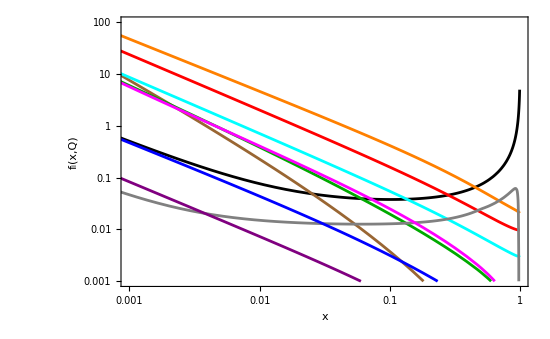

```mathematica
plot3TeV = LogLogPlot[{
μPDFpart[μL,Qplot][x]+μPDFpart[μR,Qplot][x],
μPDFpart[γp,Qplot][x]+ μPDFpart[γm,Qplot][x],
μPDFpart[gp,Qplot][x]+ μPDFpart[gm,Qplot][x],
μPDFpart[Wmp,Qplot][x]+ μPDFpart[Wmm,Qplot][x],
μPDFpart[Wpp,Qplot][x]+ μPDFpart[Wpm,Qplot][x],
μPDFpart[Zp,Qplot][x]+ μPDFpart[Zm,Qplot][x],
μPDFpart[νμ,Qplot][x],
 μPDFpart[νeb,Qplot][x],
μPDFpart[eL,Qplot][x]+μPDFpart[eR,Qplot][x],
qPDF[x] 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

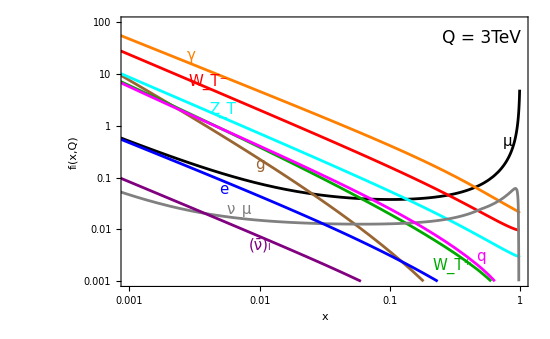

```mathematica
Show[plot3TeV,
Graphics[Text[Style["Q = 3TeV",17,Black],{Log[0.5],Log[50]}]],
Graphics[Text[Style["γ",15,Orange],{Log[0.003],Log[23]}]],
Graphics[Text[Style["W_T^-",15,Red],{Log[0.004],Log[7]}]],
Graphics[Text[Style["W_T^+",15,Darker[Green]],{Log[0.3],Log[0.002]}]],
Graphics[Text[Style["Z_T",15,Cyan],{Log[0.0052],Log[2]}]],
Graphics[Text[Style["g",15,Brown],{Log[0.01],Log[0.18]}]],
Graphics[Text[Style["μ",15,Black],{Log[0.8],Log[0.5]}]],
Graphics[Text[Style["(ν̄)_l",15,Purple],{Log[0.01],Log[0.005]}]],
Graphics[Text[Style["ν_μ",15,Gray],{Log[0.007],Log[0.023]}]],
Graphics[Text[Style["e",15,Blue],{Log[0.0053],Log[0.06]}]],
Graphics[Text[Style["q",15,Magenta],{Log[0.5],Log[0.003]}]]
]
```

-------------------------------------------------------

Polarization of the muon PDF:

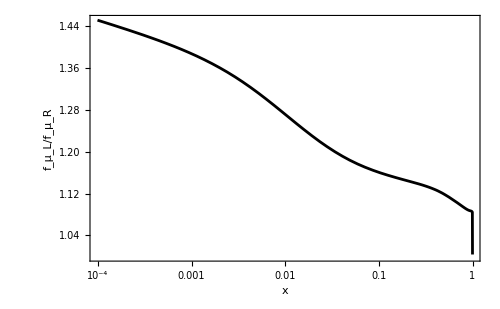

```mathematica
plotψpol=LogLinearPlot[{(μPDFpart[μL,Qplot][x])/(μPDFpart[μR,Qplot][x])},{x,0.000099,1},PlotStyle->{Black},PlotRange->{{0.000099,1},Automatic},Frame->True,AxesOrigin->{0,1},FrameLabel->{"x","f_μ_L/f_μ_R"},RotateLabel->True,BaseStyle->Directive[16,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->500]
```

## Parton luminosities for a μ- μ+ collider

Parton luminosity for a μ- <> μ+ collider as function of the partonic  invariant mass m, which also fixes the PDF factorization scale as m/2.

```mathematica
Lμmμp[part1_,part2_,mμμ_,sqrts0_]:=NIntegrate[1/x μPDFpart[part1,mμμ/2][x]μbPDFpart[part2,mμμ/2][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
Lμmμp[μL,μLb,1000,3000]
```

0.0105059

```mathematica
Lμmμp[Wmm,Wpp,500,3000]
```

0.000808942